# Изпит по КЧМ, И4, РБ, Име: Мкртич Чивиджян, Фак. № 2001261044

## Задача 4:

Условие:
y’ = y-(a+1)sin(x)  , y(0) = b,  x ϵ [0, 0.5]

```mathematica
Clear[x,y]
DSolve[{y'[x]==y[x]-(4+1)Sin[x], y[0]==4}, y[x],x]
```

```mathematica
{{y[x]->1/2 (3 ⅇ^x+5 Cos[x]+5 Sin[x])}}
```

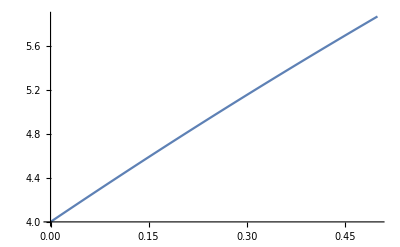

```mathematica
yt[x_]:=1/2 (3 ⅇ^x+5 Cos[x]+5 Sin[x])
Plot[yt[x], {x, a,b}]
```

### a) n = a + b + 3 = 7

```mathematica
(*Въвеждаме условието на задачата*)
a = 0.;b=0.5;
x = a;
y = 4.;
f[x_,y_] := y-(4+1)Sin[x]

(*Точно решение*)
yt[x_]:=1/2 (3 ⅇ^x+5 Cos[x]+5 Sin[x])

(*Съставяме мрежата*)
n = 7; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]

(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^2]
Print["Теоретичната глобална грешка е ", h]

(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
Print["i = ", i, ",| x_i = ", x, ",| y_i = ", y, ",| f_i = ", f[x,y] , ",| y_(:0442:043e:0447:043d:043e) = ", yt[x], ",| истинска грешка = ", Abs[y-yt[x]]];
y = y + h*f[x,y];
x = x + h;
]
```

Мрежата е с n = 7 и стъпка h = 0.0714286

Теоретичната локална грешка  е 0.00510204

Теоретичната глобална грешка е 0.0714286

i = 0,| x_i = 0.,| y_i = 4.,| f_i = 4.,| y_точно = 4.,| истинска грешка = 0.

i = 1,| x_i = 0.0714286,| y_i = 4.28571,| f_i = 3.92888,| y_точно = 4.28311,| истинска грешка = 0.00260736

i = 2,| x_i = 0.142857,| y_i = 4.56635,| f_i = 3.85449,| y_точно = 4.56081,| истинска грешка = 0.00553825

i = 3,| x_i = 0.214286,| y_i = 4.84167,| f_i = 3.77842,| y_точно = 4.83291,| истинска грешка = 0.00875883

i = 4,| x_i = 0.285714,| y_i = 5.11156,| f_i = 3.70234,| y_точно = 5.09933,| истинска грешка = 0.0122293

i = 5,| x_i = 0.357143,| y_i = 5.37601,| f_i = 3.62802,| y_точно = 5.36011,| истинска грешка = 0.0159033

i = 6,| x_i = 0.428571,| y_i = 5.63515,| f_i = 3.55729,| y_точно = 5.61543,| истинска грешка = 0.019728

i = 7,| x_i = 0.5,| y_i = 5.88925,| f_i = 3.49212,| y_точно = 5.8656,| истинска грешка = 0.0236433

### б)

Точността на полученото е решение е: "y_(:0442:043e:0447:043d:043e) = 5.8656

### в)

Извод : Не можем да намерим точно решение с аналитичен метод

### д) n = 7

```mathematica
(*Въвеждаме условието на задачата*)
a = 0.;b=0.5;
x = a;
y = 4.;
f[x_,y_] := y-(4+1)Sin[x]

(*Точно решение*)
yt[x_]:=1/2 (3 ⅇ^x+5 Cos[x]+5 Sin[x])

(*Съставяме мрежата*)
n = 7; h = (b - a)/n;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]

(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]


(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
x12 = x + h/2;
y12 = y + h/2 f[x,y];
Print["i = ", i, ",| x_i = ", x, ",| y_i = ", y, ",| f_i = ", f[x,y]  , ",| x_(i + 1/2) = ", x12, ",| y_(i + 1/2) = ", y12, ",| f_(i + 1/2) = ", f[x12,y12]  ",| y_(:0442:043e:0447:043d:043e) = ", yt[x], ", истинска грешка = ", Abs[y-yt[x]]];
y = y + h*f[x12,y12];
x = x + h;

]
```

Мрежата е с n = 7 и стъпка h = 0.0714286

Теоретичната локална грешка  е 0.000364431

Теоретичната глобална грешка е 0.00510204

i = 0,| x_i = 0.,| y_i = 4.,| f_i = 4.,| x_(i + 1/2) = 0.0357143,| y_(i + 1/2) = 4.14286,| f_(i + 1/2) = 3.96432 ,| y_точно = 4., истинска грешка = 0.

i = 1,| x_i = 0.0714286,| y_i = 4.28317,| f_i = 3.92633,| x_(i + 1/2) = 0.107143,| y_(i + 1/2) = 4.42339,| f_(i + 1/2) = 3.8887 ,| y_точно = 4.28311, истинска грешка = 0.0000590497

i = 2,| x_i = 0.142857,| y_i = 4.56093,| f_i = 3.84907,| x_(i + 1/2) = 0.178571,| y_(i + 1/2) = 4.6984,| f_(i + 1/2) = 3.81028 ,| y_точно = 4.56081, истинска грешка = 0.000120439

i = 3,| x_i = 0.214286,| y_i = 4.83309,| f_i = 3.76985,| x_(i + 1/2) = 0.25,| y_(i + 1/2) = 4.96773,| f_(i + 1/2) = 3.73071 ,| y_точно = 4.83291, истинска грешка = 0.000183033

i = 4,| x_i = 0.285714,| y_i = 5.09957,| f_i = 3.69036,| x_(i + 1/2) = 0.321429,| y_(i + 1/2) = 5.23137,| f_(i + 1/2) = 3.65176 ,| y_точно = 5.09933, истинска грешка = 0.000245556

i = 5,| x_i = 0.357143,| y_i = 5.36041,| f_i = 3.61242,| x_(i + 1/2) = 0.392857,| y_(i + 1/2) = 5.48943,| f_(i + 1/2) = 3.57528 ,| y_точно = 5.36011, истинска грешка = 0.00030658

i = 6,| x_i = 0.428571,| y_i = 5.61579,| f_i = 3.53793,| x_(i + 1/2) = 0.464286,| y_(i + 1/2) = 5.74214,| f_(i + 1/2) = 3.50322 ,| y_точно = 5.61543, истинска грешка = 0.000364515

i = 7,| x_i = 0.5,| y_i = 5.86602,| f_i = 3.46889,| x_(i + 1/2) = 0.535714,| y_(i + 1/2) = 5.98991,| f_(i + 1/2) = 3.43763 ,| y_точно = 5.8656, истинска грешка = 0.000417602